# 2. The Truncated Wigner Approximation for Bose Condensates

## An implementation in Mathematica

## Jacques Tempere, September 2022 TQC, Dept. Fysica, Universiteit Antwerpen

This notebook follows "Solving the Gross-Pitaevskii equation in Mathematica" by the same author. In that previous notebook, a Gross-Pitaevskii (GP) solver was presented and explained. However, the GP equation does not take quantum fluctuations into account, it is basically a classical field theory for the macroscopically occupied condensate mode. In applications where the correlations in the bose field are of interest, a more advanced approach is needed. The approach that I will implement here is the “Truncated Wigner Approximation”, and for the Gross-Pitaevskii equation it was developed and explained pedagogically in:

“Dynamical quantum noise in trapped Bose-Einstein condensates”, M. J. Steel, M. K. Olsen, L. I. Plimak, P. D. Drummond, S. M. Tan, M. J. Collett, D. F. Walls, and R. Graham, Physical Review A 58, 4824-4835 (1998),

and the version I will use here was described in

“The truncated Wigner method for Bose condensed gases: limits of validity and application”, A. Sinatra, C. Lobo, Y. Castin, 	Journal of Physics B 35, 3599-3631 (2002); preprint on arXiv,

and in the references cited therein.

## Introduction

Whereas in Newtonian physics a particle follows a single trajectory fixed for all times by the initial conditions, in quantum mechanics all trajectories matter. Expectation values are to be computed as a weighted average over all the trajectories. Feynman’s path integral weight for a single trajectory is a phase factor, with the phase given by the classical action divided by Planck’s constant.

This is also the distinction between a classical field and a quantum field. In classical field theory, we are interested in the (often unique) solution of the field equation. In quantum field theory, all field configurations matter, and we are interested in calculating expectation values or correlations as weighted averages over all the field configurations. Again, the weight is a phase factor, where now the classical field action is used.

Back to the Newtonian trajectory - considered now as trajectories in phase space. The initial conditions for position and momentum become subject to the uncertainty relation in quantum mechanics. Rather than a single starting point in phase space, the initial state has to be specified as a distribution of points with widths both in the position coordinate and the momentum coordinate in phase space. This, in essence, is the Wigner distribution.

The time evolution of the Wigner distribution can be computed from the Heisenberg equations of motion of the Bose field, and allows a semiclassical approximation: each point of the initial state Wigner distribution follows the classical trajectory of motion. All the “quantum-ness” is programmed into the initial distribution in phase space. This is the “Truncated Wigner Approximation”: it neglects quantum jumps but is often quite able to capture the quantum fluctuations anyway (for its limits of applicability I refer to the paper mentioned above).

How does it work for a condensate? Here, our “Bose field” is dominated by a classical field contribution: the ground state of the Gross-Pitaevskii equation. This is the initial state that we will subject to perturbations, and compute the time evolution of. In quantum field theory we know that it is not only this classical solution that matters, but that we have a distribution of field configurations around it in phase space that will also contribute strongly. To set up this quantum fluctuation ensemble, we need to add quantum noise to the classical solution. This ensemble can then be propagated using the Gross-Pitaevskii equation. The final time ensemble can then be used to calculate expectation values and correlation values.

Summarizing, the scheme is:
1. Find the “classical” initial state wavefunction of the Gross-Pitaevskii equation (for example, the GP ground state at time zero).
2. Add quantum noise to create and ensemble of initial wavefunctions
3. Evolve each of these initial wavefunctions using the GP equation, to obtain an ensemble of final wavefunctions
4. Average the quantity that you want to calculate over the final ensemble.

## Initialization

The example problem that we will look at is the sudden switching on of an external potential, such as the one that was simulated in the notebook on “Solving the Gross-Pitaevskii equation in Mathematica”. We’ll also use the same system parameters - for a description of the choice of these parameters, please consult the preceding work note.

Please also note that we  use units ℏ = m = ξ = 1 where ξ is the healing length of the condensate .

```mathematica
L=50.;
npoints=2^9;
Δx=L/npoints;
```

```mathematica
xgrid=Table[ (j-1) Δx-L/2, {j,1,npoints}];
kgrid=Table[ (j-1) (2 π)/L-π/Δx, {j,1,npoints}];
```

```mathematica
Natoms=10*npoints ;
```

```mathematica
g = L/Natoms ;
```

```mathematica
Δt = 0.1 Δx^2 ;
```

We use, as before, a box potential to confine the atoms to a region of size L = 50 ξ (specified above). The potential is:

```mathematica
Vbox=5Chop[Table[ Exp[-2.(x-L/2.)^2]+Exp[-2.(x+L/2.)^2], {x,xgrid}]];
```

## 1. Find the classical GP initial wave function

We start by a good initial guess,

```mathematica
ψguess0=√(Natoms/L) Table[ -Tanh[(x-L/2.)/Sqrt[2.]]*Tanh[(x+L/2.)/Sqrt[2.]], {x,xgrid}];
normalization=Total[ Table[ (Abs[ψguess0[[j]]]^2+Abs[ψguess0[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]];
ψguess=√(Natoms/normalization)ψguess0;
```

Then we perform an imaginary time evolution of the GP equation to let this guess converge to the ground state in the box. This algorithm is again taken from the previous work note.

```mathematica
kinUim=Table[ Exp[-k^2/2 Δt], {k,kgrid}]   (*construct kinetic operator*);
ψold=ψguess;
Do[
potUim=MapThread[ Exp[-(#1 + g Abs[#2]^2-1.)Δt]&, {Vbox,ψold} ];
ψFTold=RotateRight[Fourier[ ψold ],npoints/2]   (*to reciprocal space*) ;
ψFTnew=MapThread[ Times, {kinUim,ψFTold}]   (*kinetic part of the time evolution*);
ψinterim=InverseFourier[RotateLeft[ ψFTnew, npoints/2]]   (*back to real space*);
ψnew= MapThread[ Times,{potUim,ψinterim} ]   (*potential part of the time evolution*);
norm=Total[ Table[ (Abs[ψnew[[j]]]^2+Abs[ψnew[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]];
ψold=√(Natoms/norm)ψnew,
{timestep,1,2000}] //Timing
```

{2.84375,Null}

```mathematica
ψGP=ψold;
```

The computation did not change our guess much, so it was already a fine guess. We’ve obtained the GP solution for the ground state in the flat-bottom box trap.

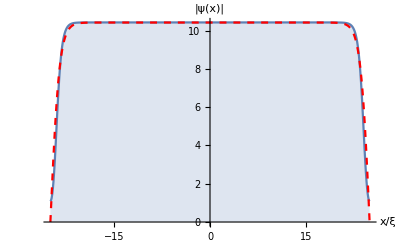

```mathematica
Show[
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψGP]} ],{{L/2,Abs[First[ψGP]]}}] , AxesLabel->{"x/ξ","|ψ(x)|"}, Joined->True, Filling->Bottom, PlotRange->All],
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψguess]} ],{{L/2,Abs[First[ψguess]]}}], Joined->True,PlotStyle->{Dashed,Red}] ]
```

## 2. Add the quantum noise

Next, quantum noise has to be added the GP solution found above, ψ_GP, to create an “Wigner” ensemble of initial wave functions ψ_W. This is done through the following formula, which requires some explanation:

ψ_W(x)=ψ_GP(x) + ∑_(k≠0) (α_k u_k e^ikx/(√L)+α_k^*v_k e^-ikx/(√L)).

The sum runs over all the Bogoliubov-de Gennes (BdG) excitation modes (except the zero mode). For our flat-bottom box potential, we have a uniform condensate, so the Bogoliubov modes are plane waves and the wave numbers of our “kgrid” are good mode indices (the edge effect at the sides of the box will be neglected). The modes are “particle-hole” mixtures with Bogoliubov coefficients u_k and v_k. They are populated by the Gaussian random noise α_k.

### Bogoliubov coefficients u_k and v_k

The Bogoliubov coefficients u_k, v_k are are related to the kinetic energy E_k=k^2/2 and the Bogoliubov energy ϵ_k=√(E_k(E_k+2g n)) via

u_k ± v_k = (E_k/ϵ_k)^(±(1/2))

In our units, E_k/ϵ_k=√(k^2/(k^2+4)). We can then create the list  of u’s and v’s from our list of k values:

```mathematica
uvlist=Table[ If[kval==0, {0,0}, With[ {Eoverϵ=Sqrt[kval^2/(kval^2+4.)]},  
{0.5(Eoverϵ^(1/2)+Eoverϵ^(-1/2)), 0.5(Eoverϵ^(1/2)-Eoverϵ^(-1/2))}]], {kval,kgrid}];
```

Only in k = 0 this does not work, we won’t need that value so we set it to zero. This will drop the term from the k-sum as well. Another way to compute this would be to use

u_k=√(1/2((E_k+g n)/ϵ_k+1))

v_k=-√(1/2((E_k+g n)/ϵ_k-1))

This yields exactly the same results .

### Random noise

The α_k are independent complex Gaussian random variables, with mean zero ⟨α_k⟩=0 and variance

⟨(|α_k|)^2⟩=1/(2 tanh(ϵ_k/(2 k_B T)))

As the temperature T tends to zero, this variance does not vanish but tends to 1/2. At low temperatures, only the low-energy modes get a broader variance, indicating the thermal fluctuations that appear on top of the quantum fluctuations.

```mathematica
αlist=RandomVariate[NormalDistribution[0.,0.5],npoints] + ⅈ RandomVariate[NormalDistribution[0.,0.5],npoints] ;
```

Here we just work with 0.5 variance (or √0.5 standard deviation, the T = 0 case) . The cloud of α values are shown below in the complex plane:

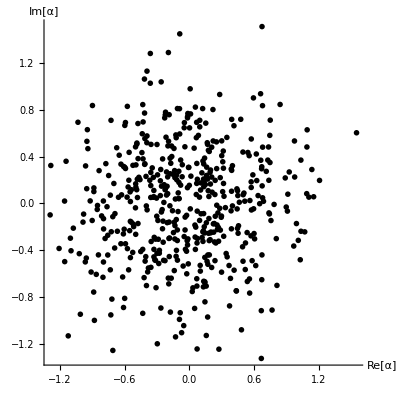

```mathematica
Show[ Graphics[  {AbsolutePointSize[4],Point[ Map[({Re[#],Im[#]})&, αlist]]}  ], Axes->True, AxesLabel->{"Re[α]","Im[α]"}, AxesStyle->Black]
```

```mathematica
StandardDeviation[ Map[(Abs[#]^2)&, αlist]]
```

0.500056

### Wigner ensemble

To make an element of the Wigner ensemble, add quantum noise to the GP wavefunction using  the above formula. For each x point we need to compute the sum

∑_(k≠0) (α_k u_k e^ikx/(√L)+α_k^*v_k e^-ikx/(√L))

```mathematica
ψnoise=Table[ 
1/(√L)Total[MapThread[  ( #1  #2[[1]] Exp[ⅈ #3 xval] +  Conjugate[#1] #2[[2]] Exp[-ⅈ #3 xval])&,   {αlist, uvlist, kgrid}] ],
{xval,xgrid} ];  //Timing
```

{0.953125,Null}

This noise is added to the original GP solution to obtain a member of the ensemble

```mathematica
ψW=ψGP+ψnoise;
```

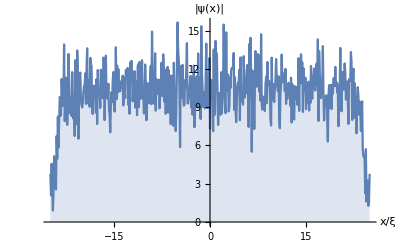

```mathematica
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψW]} ],{{L/2,Abs[First[ψW]]}}] , AxesLabel->{"x/ξ","|ψ_W(x)|"}, Joined->True, Filling->Bottom, PlotRange->All]
```

Each Bogoliubov mode is populated by noise with an amplitude of 1/2 . So, that means that ψ_W is no longer normalized to the proper number of particles. In this particular realization there is an excess of

```mathematica
Norm[ψW]^2  Δx -Natoms        (*simple sum for the integral*)
```

244.887

```mathematica
(*or with trapezium rule:*)
```

```mathematica
Total[ Table[ (Abs[ψW[[j]]]^2+Abs[ψW[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]]-Natoms
```

244.073

Since there are npoints=512 modes, we expect npoints/2 = 256 additional atoms in the average ψ_W in our example. This is something to keep in mind when calculating expectation values, we have to correct for the 1/2 occupation we added on average. In fact, the atoms now in the noncondensed “noise” part must come from the condensate. So we’d have to suitable renormalize the condensate wavefunction to take into account this depletion.

Castin and co-workers, in the papers cited in the opening paragraph, described how to take it properly into account (in a computationally intensive way). Apart from the full calculation, there’s other options of course: 
(1) neglect depletion, assuming it small enough in comparison to the total number of condensed atoms (i.e. we are in the weakly interacting regime).
(2) take it into account approximately, by renormalizing ψ_W in a naive way so that for each element in the ensemble the number of particles is correct.
(3) find a way to calculate the correction term only for the quantities you’re interested in, in the end. Since we’re taking averages, those correction terms may be easier to estimate in average than the depletion for each individual ensemble member.

Here we will take route number 3. For example, as we calculate the density, we need to compute the average over the ensemble in

n(x) = ⟨ψ_W^*ψ_W⟩ - 1/(2 Δx)

From this average, the average additional occupation is subtracted again; this is the term -1/2 (where the Δx is our integration measure to turn the discrete sum into an the integral). Before we proceed, let’s explore option 2 in the following subsection.

### A number conserving ensemble

Rather than choosing ψ_W = ψ_GP+ψ_fl , as we did above lets choose ψ_W = a ψ_GP+ψ_fl and find the correct (real-valued) a so that ψ_W remains normalized. This naive choice corresponds to giving a weight of zero in the path integral over all the field realizations that are not properly normalized. We get
a^2 ⟨ψ_GP|ψ_GP⟩ + 2 a Re(⟨ψ_GP|ψ_fl⟩)+⟨ψ_fl|ψ_fl⟩  =N_atoms

Since we previously normalized ⟨ψ_GP|ψ_GP⟩ =N_atoms, this is also

a^2 + 2 a(Re(⟨ψ_GP|ψ_fl⟩))/N_atoms+⟨ψ_fl|ψ_fl⟩/N_atoms  =1

```mathematica
renorm=First[With[  {b=Re[(Conjugate[ψGP] . ψnoise)] Δx/Natoms, c=Chop[(Conjugate[ψnoise] . ψnoise) Δx/Natoms]},
(a /. Solve[ a^2+2 a b+c==1 &&a>0, a ])]];
```

```mathematica
ψWnormd= renorm ψGP+ψnoise;
```

The Δx in the expressions above come from our intergration measure. It checks out (up to noise below the comma, from discretizing our integral):

```mathematica
{Norm[ψWnormd]^2  Δx   ,  Natoms}
```

{5120.11,5120}

This can be computed even faster but more approximate by realizing that the overlap ⟨ψ_GP|ψ_fl⟩ is quite small (and would be zero for a fully uniform condensate), so that

```mathematica
ψWbis= Sqrt[1.- (Norm[ψnoise]^2 Δx)/Natoms ] ψGP+ψnoise ;
```

```mathematica
{Norm[ψWbis]^2  Δx   ,  Natoms}
```

{5109.89,5120}

This implements suggestion 2 from the above paragraph. We’ll explore suggestion 3 later.

## 3. Evolve the ensemble

Typically, one makes an ensemble of a few thousand or tens of thousand ψ_W samples. Each of these individual ensemble members then has to be evolved in time using the GP equation. Here, we introduce an external potential, a little bump in the middle of the box, that suddenly appears:

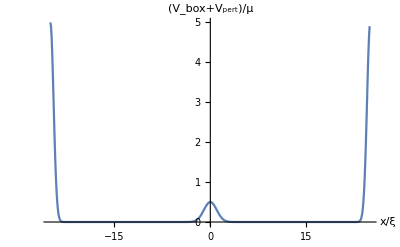

```mathematica
Vpert=0.5 Chop[Table[ Exp[-0.5 x^2], {x,xgrid}]];
ListPlot[ Transpose[{xgrid,Vbox+Vpert}], PlotRange->All, Joined->True, AxesLabel->{"x/ξ","(V_box+V_pert)/μ"}]
```

We can then use our GP evolution algorithm from the previous section to see how the element of the ensemble evolves in time. The very small damping factor that we included previously is removed.

```mathematica
kinU=Table[ Exp[-ⅈ k^2/2 Δt], {k,kgrid}]   (*construct kinetic operator*);
snapshots={ψW};
ψold=ψW;
Do[
potU=MapThread[ Exp[-ⅈ(#1 + g Abs[#2]^2-1.)Δt]&, {Vbox+Vpert,ψold} ];
ψFTold=RotateRight[Fourier[ ψold ],npoints/2]   (*to reciprocal space*) ;
ψFTnew=MapThread[ Times, {kinU,ψFTold}]   (*kinetic part of the time evolution*);
ψinterim=InverseFourier[RotateLeft[ ψFTnew, npoints/2]]   (*back to real space*);
ψnew= MapThread[ Times,{potU,ψinterim} ]   (*potential part of the time evolution*);
If[ Mod[timestep,250]==0, AppendTo[snapshots,ψnew]];
ψold=ψnew,
{timestep,1,10000}] //Timing
```

{13.0938,Null}

The norm has been (rather well) preserved in the numerical time evolution :

```mathematica
Total[ Table[ (Abs[ψnew[[j]]]^2+Abs[ψnew[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]]-Natoms
```

241.38

The whole thing for an individual realization will remain quite noisy and not much can be made out of it.

```mathematica
Manipulate[ 
ListPlot[ Join[ Transpose[ {xgrid, Abs[ snapshots[[jj]] ]} ],{{L/2,Abs[First[snapshots[[jj]]]]}}] , AxesLabel->{"x/ξ","|ψ(x)|"}, Joined->True, Filling->Bottom, PlotRange->{0,15}],
{jj,1,Length[snapshots],1}]
```

## 4. Averaging out over the ensemble

### Quantities of interest

We will look at two quantities that are usually of interest, namely the density, and the second-order correlation function. First, we need formulas linking these quantities to the average over the Wigner ensemble - this average will be denoted by a subscript W as  ⟨...⟩_W .

For the density n=⟨(ψ̂)^†ψ̂⟩, the link with the Wigner ensemble average is (in the truncated Wigner approximation):

⟨(ψ̂)^†(x)ψ̂(x) ⟩=⟨(|ψ(x)|)^2⟩_W-1/(2 Δx).

This means : compute for each member of the ensemble the modulus squared, in each grid point. Then, subtract the 1/2  we added on average to each grid point (and note that there is 1 point per grid step Δx). The 1/2 comes from the added quantum noise that broke the normalization, as explained in more detail in section 2.

The main quantity of interest is the two-point correlation function. This is where the quantum fluctuations matter! This correlation function is defined as

G_2(x,x')=⟨(ψ̂)^†(x)(ψ̂)^†(x')ψ̂(x')ψ̂(x) ⟩/(⟨(ψ̂)^†(x)ψ̂(x) ⟩⟨(ψ̂)^†(x')ψ̂(x') ⟩).

Without quantum fields, the Bose fields are just c-numbers and the two-point correlation function would be equal to 1. But they are operators, and the commutation properties make it so that ⟨(ψ̂)^†(x)(ψ̂)^†(x')ψ̂(x')ψ̂(x) ⟩ is not just the product of the two densities in the denominator.

When computing the numerator from averages over the Wigner ensemble (of complex functions) some extra terms arise from ordering the operators. Also, the 1/2 factors from the added noise appear. The truncated Wigner approximation is then:

⟨(ψ̂)^†(x)(ψ̂)^†(x')ψ̂(x')ψ̂(x) ⟩=⟨(|ψ(x)|)^2(|ψ(x')|)^2⟩_W-(1+δ_(x,x'))/(2Δx)(⟨(|ψ(x)|)^2⟩_W+⟨(|ψ(x')|)^2⟩_W)+(1+δ_(x,x'))/(4 Δx^2).

Here δ_(x,x') is the kronecker delta, equal to 1 when x and x’ refer to the same grid point, and zero otherwise. So, what we have to keep track of are actually the averages ⟨(|ψ(x)|)^2(|ψ(x')|)^2⟩_W and ⟨(|ψ(x)|)^2⟩_W , and from these two we can compute the density and the two-point correlation.